{{u[x]→C[1] MathieuC[(2 e m)/(h2 k^2),-(m v)/(h2 k^2),k x]+C[2] MathieuS[(2 e m)/(h2 k^2),-(m v)/(h2 k^2),k x]}}

{C[1] MathieuC[1,-1,x]+C[2] MathieuS[1,-1,x]}

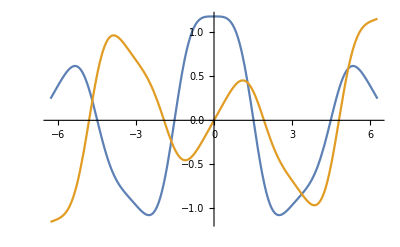

```mathematica
sol=DSolve[-h2/(2m) u''[x]-v Cos[2 k x] u[x]==e u[x],u[x],x]
u[x]/.sol/.{k->1,h2->1,m->1,e->1/2,v->1}
Plot[{MathieuC[2,1,x], MathieuS[2,1,x]},{x,-2Pi,2Pi}]
```

```mathematica
sol=DSolve[{-h2/(2m) u''[x]-v Cos[2 k x] u[x]==e u[x],u'[0]==0},u[x],x]
MathieuCharacteristicA[kp/k,-(m v)/(h2 k^2)]
```

{{u[x]→C[1] MathieuC[(2 e m)/(h2 k^2),-(m v)/(h2 k^2),k x]}}

MathieuCharacteristicA[kp/k,-(m v)/(h2 k^2)]